# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Henyey-greenstein Scattering

[Henyey and Greestein 1940] - “Diffuse radiation in the Galaxy”

```mathematica
Clear[pHG];pHG[dot_,g_]:=1/(4 Pi)(1-g^2)/((1+g^2-2g dot)^(3/2))
```

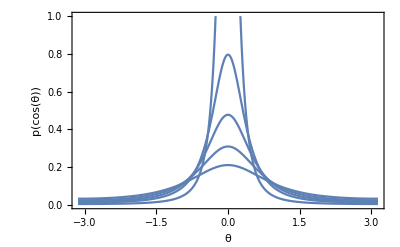

```mathematica
pHGplot=Show[
Plot[pHG[Cos[t],.8],{t,-Pi,Pi},PlotRange->{0,1}],
Plot[pHG[Cos[t],.6],{t,-Pi,Pi},PlotRange->All],
Plot[pHG[Cos[t],.5],{t,-Pi,Pi},PlotRange->All],
Plot[pHG[Cos[t],.4],{t,-Pi,Pi},PlotRange->All],
Plot[pHG[Cos[t],.3],{t,-Pi,Pi},PlotRange->All],
Frame->True,
ImageSize->400,
FrameLabel->{{p[Cos[θ]],},{θ,"Henyey-Greenstein Scattering, g = 0.3, 0.4, 0.5, 0.6, 0.8"}}]
```

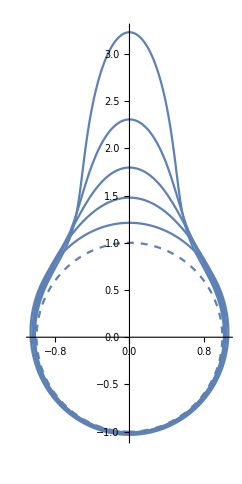

```mathematica
Show[
ParametricPlot[{Sin[t],Cos[t]}(1),{t,-Pi,Pi},PlotRange->All,PlotStyle->Dashed],
ParametricPlot[{Sin[t],Cos[t]}(1+pHG[Cos[t],0.75]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pHG[Cos[t],0.68]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pHG[Cos[t],0.6]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pHG[Cos[t],0.5]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pHG[Cos[t],0.3]),{t,-Pi,Pi},PlotRange->All]
]
```

### Normalization condition

```mathematica
Integrate[2 Pi pHG[u,g],{u,-1,1},Assumptions->g>-1&&g<1]
```

1

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pHG[u,g]LegendreP[k,u]/.k->0,{u,-1,1},Assumptions->g>-1&&g<1]
```

1

```mathematica
Integrate[2Pi(2k+1)pHG[u,g]LegendreP[k,u]/.k->1,{u,-1,1},Assumptions->g>-1&&g<1]
```

3 g

```mathematica
Integrate[2Pi(2k+1)pHG[u,g]LegendreP[k,u]/.k->2,{u,-1,1},Assumptions->g>-1&&g<1]
```

5 g^2

```mathematica
Integrate[2Pi(2k+1)pHG[u,g]LegendreP[k,u]/.k->3,{u,-1,1},Assumptions->g>-1&&g<1]
```

7 g^3

```mathematica
Integrate[2Pi(2k+1)pHG[u,g]LegendreP[k,u]/.k->4,{u,-1,1},Assumptions->g>-1&&g<1]
```

9 g^4

### sampling

```mathematica
cdf=Integrate[2 Pi pHG[u,g],{u,-1,x},Assumptions->g>-1&&g<1&&x<1]
```

((-1+g) (-1-g+√(1+g^2-2 g x)))/(2 g √(1+g^2-2 g x))

```mathematica
Solve[cdf==e,x]
```

{{x→(-1+2 e+2 g-2 e g+2 e^2 g-g^2+2 e g^2-2 e g^3+2 e^2 g^3)/(1-g+2 e g)^2}}

```mathematica
FullSimplify[%]
```

{{x→-((-1+g)^2+2 e (-1+g) (1+g^2)-2 e^2 (g+g^3))/(1+(-1+2 e) g)^2}}

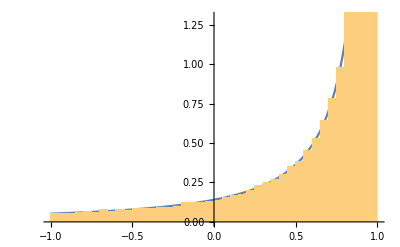

```mathematica
g=0.7;
Show[
Plot[2 Pi pHG[u,g],{u,-1,1}],
Histogram[Map[-((-1+g)^2+2 # (-1+g) (1+g^2)-2 #^2 (g+g^3))/(1+(-1+2 #) g)^2&,Table[RandomReal[],{i,1,100000}]],50,"PDF"]
]
Clear[b,g];
```

When cosine u has been sampled with random variable ξ, what is the PDF at the sampled direction in terms of ξ?

```mathematica
FullSimplify[pHG[-((-1+g)^2+2 (-1+g) (1+g^2) ξ-2 (g+g^3) ξ^2)/(1+g (-1+2 ξ))^2,g],Assumptions->-1<g<1&&0<ξ<1]
```

(1+g (-1+2 ξ))^3/(4 (-1+g^2)^2 π)